```mathematica
maxfac=5;
```

```mathematica
texp[x_]=Normal[Series[Exp[x],{x,0,maxfac}]]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120

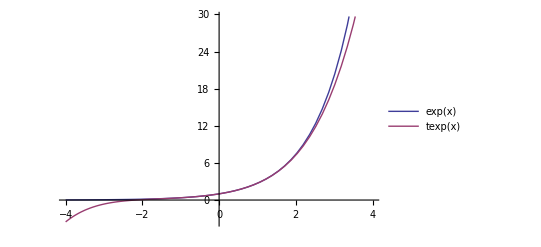

```mathematica
Plot[{Exp[x],texp[x]},{x,-4,4},PlotLegends->"Expressions"]
```

```mathematica
maxfac=3
```

3

```mathematica
coeffs=Table[Subscript[c, i],{i,0,maxfac}]
```

{c_0,c_1,c_2,c_3}

```mathematica
sqrtexp[x_]=Sum[Subscript[c, i] x^i,{i,0,maxfac}]
```

c_0+x c_1+x^2 c_2+x^3 c_3

```mathematica
sqrtexp[sqrtexp[x]]//Expand;
```

```mathematica
sqrtcoeff=CoefficientList[sqrtexp[sqrtexp[x]],x];
```

```mathematica
expcoeff=CoefficientList[Normal[Series[Exp[x],{x,0,maxfac^2}]],x];
```

```mathematica
eqns=MapThread[#1==#2&,{sqrtcoeff,expcoeff}];
```

```mathematica
NSolve[eqns[[1;;Length[coeffs]]],coeffs,Reals]
```

{{c_0→-23.5716,c_1→-1.04226×10^11,c_2→-1.46695×10^9,c_3→1.25352×10^8},{c_0→-7.20014,c_1→-26.2495,c_2→-2.25,c_3→0.171875},{c_0→0.498574,c_1→0.876383,c_2→0.247391,c_3→0.0241167},{c_0→0.573383,c_1→1.42628,c_2→-2.30487,c_3→1.94463}}

```mathematica
mysol=%[[-1]]
```

{c_0→0.573383,c_1→1.42628,c_2→-2.30487,c_3→1.94463}

```mathematica
sqrtexpc[x_]=sqrtexp[x]/.mysol
```

0.573383+1.42628 x-2.30487 x^2+1.94463 x^3

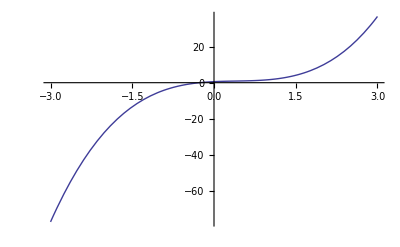

```mathematica
Plot[sqrtexpc[x],{x,-3,3}]
```

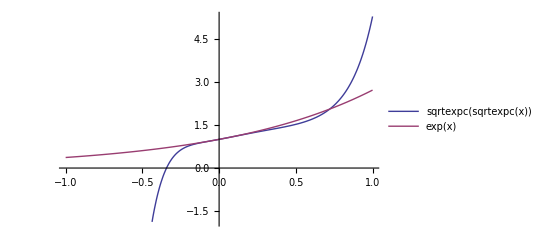

```mathematica
Plot[{sqrtexpc[sqrtexpc[x]],Exp[x]},{x,-1,1},PlotLegends->"Expressions"]
```